## Calculation of infinite sum

```mathematica
sum=Sum[1/(2n+1)^5*Tanh[(2n+1)*Pi/2],{n,0,Infinity}]
```

∑_(n=0)^∞ Tanh[1/2 (1+2 n) π]/(1+2 n)^5

```mathematica
ans=16/3-1024/Pi^5*sum
```

16/3-(1024 ∑_(n=0)^∞ Tanh[1/2 (1+2 n) π]/(1+2 n)^5)/π^5

```mathematica
N[ans]
```

2.24923

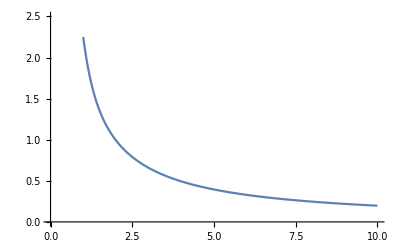

```mathematica
Plot[16/(3*x)-1024/(Pi^5*x)*Sum[1/(2n+1)^5*Tanh[(2n+1)*x*Pi/2],{n,0,Infinity}],{x,1,10}, PlotRange->{{0,10},{0,2.5}}]
```